## Equations

du_0'/dr' = -(ϵ_0'+σ_0')v_0',
dv_0'/dr' = -2/r'v_0'+(ϵ_0'-σ_0')u_0',

(d^2 σ_0')/dr'^2 = -2/r' dσ_0'/dr'+(dU'(σ_0'))/dσ_0'+(u_0')^2-(v_0')^2;
σ_0'(ϵ)=σ_1+ϵ^2/2 σ_2+O(ϵ^3);
u_0'(ϵ)=u_1+ϵ^2/2 u_2+O(ϵ^3);
v_0'(ϵ)=ϵ  v_1+O(ϵ^3);
u_2=-(ϵ_0'+σ_1)v_1;
3 v_1=(ϵ_0'-σ_1)u_1;
σ_2=1/3((dU'(σ_1))/dσ_0'+u_1'^2);
v_1=1/3(ϵ_0'-σ_1)u_1;
u_2=1/3(σ_1^2-(ϵ_0')^2)u_1

U(σ)=(σ-v)^2(s σ^2+2 t σ_v σ+t σ_v^2)
U(σ)=g^2 σ_v^4 U'(σ')
U(σ')=(σ'-1)^2(s' σ'^2+2 t' σ'+t')
σ=σ_v σ'
ϵ=g σ_v ϵ'
r'=g σ_v r
s=g^2 s'
t=g^2 t'

```mathematica
U=(σ-v)^2(s σ^2+2 t v σ+t v^2)
```

(-v+σ)^2 (t v^2+2 t v σ+s σ^2)

```mathematica
Simplify[D[U,σ]]
```

2 (-3 t v+s (v-2 σ)) (v-σ) σ

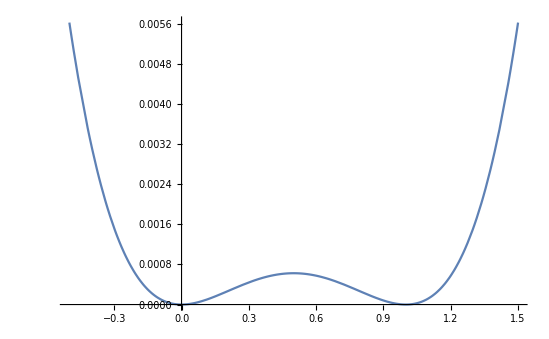

```mathematica
Plot[U/.{v->1,s->0.01,t->0.0},{σ,-0.5,1.5}]
```

```mathematica
vacs=Solve[D[U,σ]==0,σ]
```

{{σ→0},{σ→v},{σ→((s-3 t) v)/(2 s)}}

```mathematica
vacs
```

{{σ→0},{σ→v},{σ→((s-3 t) v)/(2 s)}}

```mathematica
Simplify[D[U,{σ,2}]/.vacs]
```

{2 (s-3 t) v^2,2 (s+3 t) v^2,-((s^2-9 t^2) v^2)/s}

```mathematica
Simplify[D[U,σ]/.v->1/.σ->σ0]
```

2 (-1+σ0) σ0 (3 t+s (-1+2 σ0))

```mathematica
ρ=70;
eps=10^-3;
FB=ParametricNDSolve[{
u'[r]==-(ϵ+σ[r])v[r],
v'[r]==-2/r v[r]+(ϵ-σ[r])u[r],
σ''[r]+2/r σ'[r]-(2 (-1+σ[r]) σ[r] (-s+3 t+2 s σ[r]))==u[r]^2-v[r]^2,
(*u[ρ]==((1+ϵ)ρ)/(1+√(1-ϵ^2)r)v[ρ],*)
σ[ρ]+ρ/(1+√(2 (s+3 t))ρ)σ'[ρ]==1,
σ'[eps]==eps/3(2 (-1+σ0) σ0 (3 t+s (-1+2 σ0))+u0^2),
u[eps]==eps/3(σ0^2-ϵ^2)u0,
v[eps]==1/3(ϵ-σ0)u0
},
{σ,u,v},{r,eps,ρ},{ϵ,σ0,u0,s,t}]
```

{σ→ParametricFunction[<>],u→ParametricFunction[<>],v→ParametricFunction[<>]}

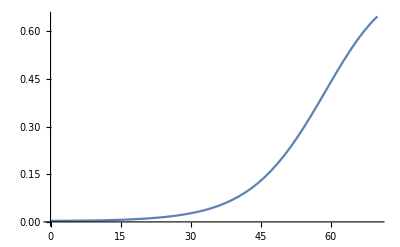

```mathematica
Plot[σ[0.5,0.1,0.01,0.01,0][r]/.FB,{r,0.001,70}]
```

## B-Splines

```mathematica
σ0[r_]:=1-1.4 ⅇ^(-(r/10)^2);
u0[r_]:=1/3 ⅇ^(-((r-1.5)/10)^2);
v0[r_]:=(r/10)^2 ⅇ^(-2(r/10)^2);
```

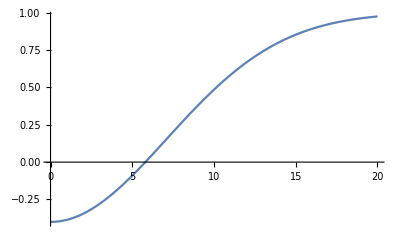

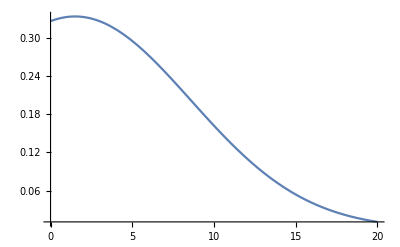

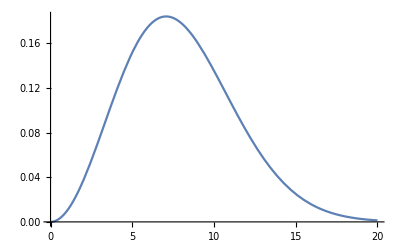

```mathematica
box=20;
Plot[σ0[r],{r,0,box},PlotRange->Full]
Plot[u0[r],{r,0,box},PlotRange->Full]
Plot[v0[r],{r,0,box},PlotRange->Full]
```

```mathematica
Bag[s_,t_,ϵ_,R_,n_]:=(
h=R/n;
dU[σ_]:=2 (-3 t 1+s (1-2 σ)) (1-σ) σ;
(*σ equations*)
eqσ[0]=6(σ[1]-σ[0])==6 h^2(dU[2/3 σ[0]+1/3 σ[1]]+((*1/6 u[-1]+*)2/3 u[0]+1/6 u[1])^2-(1/6 v[-1]+2/3 v[0]+1/6 v[1])^2);(*0-th poin equation (1-st b.c. is already absorbed)*)
Table[eqσ[i]=(6-3h 2/(i h))σ[i-1]-12 σ[i]+(6 +3h 2/(i h))σ[i+1]==6 h^2(dU[1/6 σ[i-1]+2/3 σ[i]+1/6 σ[i+1]]+(1/6 u[i-1]+2/3 u[i]+1/6 u[i+1])^2-(1/6 v[i-1]+2/3 v[i]+1/6 v[i+1])^2),{i,1,n-1}];
eqσ[n]=(6-3h 2/(n h))σ[n-1]-12 σ[n]+(6 +3h 2/(n h))σ[n+1]==6 h^2(dU[1/6 σ[n-1]+2/3 σ[n]+1/6 σ[n+1]]+(1/6 u[n-1]+2/3 u[n]+1/6 u[n+1])^2-(1/6 v[n-1]+2/3 v[n](*+1/6v[i+1]*))^2);
(*1-n-th equations*)
eqσ[n+1]=1/6(σ[n-1]+4σ[n]+σ[n+1])+R/(1+√(2(s+3 t))R)1/(2h)(-σ[n-1]+σ[n+1])==1;(*2-nd b.c.*)
(*n+2 equations for c[0],..,c[n+1] coeficients*)
(*u equations*)
equ[0]=-1/(2h)(-u[1])==-(ϵ+(1/6 σ[-1]+2/3 σ[0]+1/6 σ[1]))(1/6 v[-1]+2/3 v[0]+1/6 v[1]);
Table[equ[i]=1/(2h)(-u[i-1]+u[i+1])==-(ϵ+(1/6 σ[i-1]+2/3 σ[i]+1/6 σ[i+1]))(1/6 v[i-1]+2/3 v[i]+1/6 v[i+1]),{i,1,n-1}];(*n equations*)
equ[n]=1/(2h)(-u[n-1]+u[n+1])==-(ϵ+(1/6 σ[n-1]+2/3 σ[n]+1/6 σ[n+1]))(1/6 v[n-1]+2/3 v[n](*+1/6v[i+1]*));
equ[n+1]=1/6 u[n-1]+2/3 u[n]+1/6 u[n+1]==((1+ϵ) R)/(1+√(1-ϵ^2)R)(1/6 v[n-1]+2/3 v[n](*+1/6v[i+1]*));(*b.c. for u*)
(*n+2 eq-s for u[0],..,u[n+1]*)
(*v equations*)
eqv[-1]=v[-1]+4v[0]+v[1]==0;(*1-st b.c.*)
eqv[0]=1/(2h)(-v[-1]+v[1])==(v[-1]-v[1])/h+(ϵ-(1/6 σ[-1]+2/3 σ[0]+1/6 σ[1]))((*1/6 u[-1]+*)2/3 u[0]+1/6 u[1]);(*0-th point equation*)
Table[eqv[i]=1/(2h)(-v[i-1]+v[i+1])==-2/(i h)(v[i-1]+4v[i]+v[i])/6+(ϵ-(1/6 σ[i-1]+2/3 σ[i]+1/6 σ[i+1]))(1/6 u[i-1]+2/3 u[i]+1/6 u[i+1]),{i,1,n-1}];(*n-1 equations*)
eqv[n]=-1/(2h)v[n-1]==-2/(i h)(v[n-1]+4v[n])/6+(ϵ-(1/6 σ[n-1]+2/3 σ[n]+1/6 σ[n+1]))(1/6 u[n-1]+2/3 u[n]+1/6 u[n+1]);
(*Loking for initial approximation*)
(*initial σ*)
Table[σineq[i]=1/6 σin[i-1]+2/3 σin[i]+1/6 σin[i+1]==σ0[i h],{i,0,n}];
σineq[-1]=σin[-1]==σin[1]; σineq[n+1]=σin[n-1]==σin[n+1];
σapprox=Table[σin[j],{j,-1,n+1}]/.NSolve[Table[σineq[i],{i,-1,n+1}],Table[σin[j],{j,-1,n+1}]];
(*initial u*)
Table[uineq[i]=1/6 uin[i-1]+2/3 uin[i]+1/6 uin[i+1]==u0[i h],{i,1,n}];
uineq[0]=2/3 uin[0]+1/6 uin[1]==u0[0]; uineq[n+1]=uin[n-1]==uin[n+1];
uapprox=Table[uin[j],{j,0,n+1}]/.NSolve[Table[uineq[i],{i,0,n+1}],Table[uin[j],{j,0,n+1}]];
(*initial v*)
Table[vineq[i]=1/6 vin[i-1]+2/3 vin[i]+1/6 vin[i+1]==v0[i h],{i,0,n-1}];
vineq[-1]=1/6 vin[-1]+2/3 vin[0]+1/6 vin[1]==0;vineq[n]=-vin[n-2]+vin[n]==0;
vapprox=Table[vin[j],{j,-1,n}]/.NSolve[Table[vineq[i],{i,-1,n}],Table[vin[j],{j,-1,n}]];
(*Solving*)
(*sol=FindRoot[
Join[Table[eqσ[i],{i,0,n+1}],Table[equ[i],{i,1,n+1}],Table[eqv[i],{i,-1,n}]],Join[Table[{σ[k],σapprox[[1,1+k]]},{k,0,n+1}],Table[{u[k],uapprox[[1,1+k]]},{k,0,n+1}],Table[{v[k],vapprox[[1,2+k]]},{k,-1,n}]]
];*)
)
```

```mathematica
b[-1]=(h-δ)^3/(6 h^3);
b[0]=(-3(h-δ)^3+3(h-δ)^2 h+3(h-δ)h^2+h^3)/(6 h^3);
b[1]=(-3(δ)^3+3(δ)^2 h+3(δ)h^2+h^3)/(6 h^3);
b[2]=(δ)^3/(6 h^3);
Table[Expand[Simplify[2/δ D[b[i],δ]]],{i,-1,2}]
Table[db[i]=Expand[Simplify[D[b[i],δ]]],{i,-1,2}]
Table[ddb[i]=Expand[Simplify[D[b[i],{δ,2}]]],{i,-1,2}]
Simplify[(c1)db[-1]+c0 db[0]+c1 db[1]+c2 db[2]]
```

{2/h^2-1/(h δ)-δ/h^3,-4/h^2+(3 δ)/h^3,2/h^2+1/(h δ)-(3 δ)/h^3,δ/h^3}

{-1/(2 h)+δ/h^2-δ^2/(2 h^3),-(2 δ)/h^2+(3 δ^2)/(2 h^3),1/(2 h)+δ/h^2-(3 δ^2)/(2 h^3),δ^2/(2 h^3)}

{1/h^2-δ/h^3,-2/h^2+(3 δ)/h^3,1/h^2-(3 δ)/h^3,δ/h^3}

(δ (-4 c0 h+4 c1 h+3 c0 δ-4 c1 δ+c2 δ))/(2 h^3)

```mathematica
Limit[Simplify[((c1)ddb[-1]+c0 ddb[0]+c1 ddb[1]+c2 ddb[2])+2/δ((c1)db[-1]+c0 db[0]+c1 db[1]+c2 db[2])],δ->0]
```

(2 (-3 c0 h+3 c1 h))/h^3

```mathematica
σ0[r_]:=1-1.2 ⅇ^(-(r/3)^2)
u0[r_]:=0.9 ⅇ^(-(r/3)^2)
```

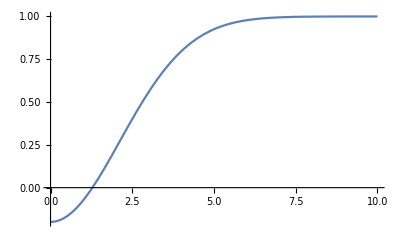

```mathematica
Plot[σ0[r],{r,0,10}]
```

```mathematica
Bag[s_,t_,ϵ_,R_,n_]:=(
h=R/n;
dU[σ_]:=2 (-3 t 1+s (1-2 σ)) (1-σ) σ;
(*σ equations*)
eqσ[0]=6(σ[1]-σ[0])==h^2(dU[2/3 σ[0]+1/3 σ[1]]+(2/3 u[0]+1/3 u[1])^2);
Table[eqσ[i]=(1-h/2 2/(i h))σ[i-1]-2 σ[i]+(1 +h/2 2/(i h))σ[i+1]==h^2(dU[1/6 σ[i-1]+2/3 σ[i]+1/6 σ[i+1]]+(1/6 u[i-1]+2/3 u[i]+1/6 u[i+1])^2-(-(-u[i-1]/(2h)+u[i+1]/(2h))/(ϵ+1/6 σ[i-1]+2/3 σ[i]+1/6 σ[i+1]))^2),{i,1,n}];
eqσ[n+1]=1/6(σ[n-1]+4σ[n]+σ[n+1])+R/(1+√(2(s+3 t))R)1/(2h)(-σ[n-1]+σ[n+1])==1;
(*u equations*)
equ[0]=6(u[1]-u[0])==h^2((2/3 σ[0]+1/3 σ[1])^2-ϵ^2)(2/3 u[0]+1/3 u[1]);
Table[equ[i]=(1-h/2 2/(i h))u[i-1]-2 u[i]+(1 +h/2 2/(i h))u[i+1]==h^2(((1/6 σ[i-1]+2/3 σ[i]+1/6 σ[i+1])^2-ϵ^2)(1/6 u[i-1]+2/3 u[i]+1/6 u[i+1])+((-σ[i-1]/(2h)+σ[i+1]/(2h))/(ϵ+1/6 σ[i-1]+2/3 σ[i]+1/6 σ[i+1]))(-u[i-1]/(2h)+u[i+1]/(2h))),{i,1,n}];
equ[n+1]=(1/6(√(1-ϵ^2)+1/R)-1/(2h))u[n-1]+2/3(√(1-ϵ^2)+1/R)u[n]+(1/6(√(1-ϵ^2)+1/R)+1/(2 h))u[n+1]==0;
(*initial approximation for σ*)
Table[σineq[i]=1/6 σin[i-1]+2/3 σin[i]+1/6 σin[i+1]==σ0[i h],{i,0,n}];
σineq[-1]=σin[-1]==σin[1]; σineq[n+1]=σin[n-1]==σin[n+1];
σinappr=(*Table[σin[j],{j,-1,n+1}]/.*)NSolve[Table[σineq[i],{i,-1,n+1}],Table[σin[j],{j,-1,n+1}]];
(*initial approximation for u*)
Table[uineq[i]=1/6 uin[i-1]+2/3 uin[i]+1/6 uin[i+1]==u0[i h],{i,0,n}];
uineq[-1]=uin[-1]==uin[1];uineq[n+1]=uin[n-1]==uin[n+1];
uinappr=(*Table[σin[j],{j,-1,n+1}]/.*)NSolve[Table[uineq[i],{i,-1,n+1}],Table[uin[j],{j,-1,n+1}]];
(*Solver*)
equations=Join[Table[eqσ[i],{i,0,n+1}],Table[equ[i],{i,0,n+1}]];
variables=Join[Table[{σ[i],σin[i]},{i,0,n+1}],Table[{u[i],uin[i]},{i,0,n+1}]]/.σinappr/.uinappr;
sol=FindRoot[equations,variables[[1,1]]];
σprofile=Table[{i h,1/6(σ[i-1]+4 σ[i]+σ[i+1])},{i,0,n}]/.σ[-1]->σ[1]/.sol;
uprofile=Table[{i h,1/6(u[i-1]+4 u[i]+u[i+1])},{i,0,n}]/.u[-1]->u[1]/.sol;
)
```

```mathematica
Bag[0.01,0,0.5,24,300]
```

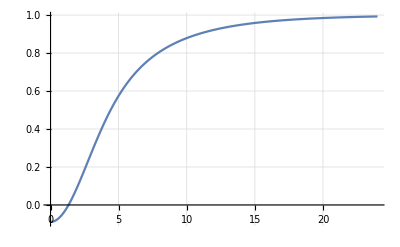

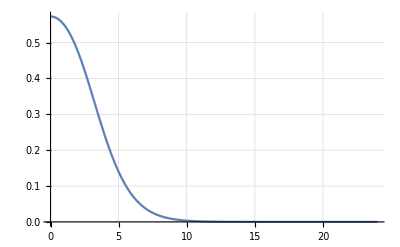

```mathematica
ListLinePlot[σprofile,PlotRange->Full,GridLines->Automatic]
ListLinePlot[uprofile,PlotRange->Full,GridLines->Automatic]
```